```mathematica
DiffurStruc[func_,arg_,cprFunc_,ccur_]:={func'[arg]-ccur-cprFunc[func[arg]]==0};
DiffurIni[func_,InitialPoint_,InitialValue_]:={func[InitialPoint]==InitialValue};
Diffur[func_,arg_,cprFunc_,ccur_,InitialPoint_,InitialValue_]:=Flatten[
{DiffurStruc[func,arg,cprFunc,ccur],DiffurIni[func,InitialPoint,InitialValue]}];
CommonCPR[ccur_, cprFunc_, InitialPoint_,InitialValue_, {arg_,lowRange_,upperRange_}]:=
NDSolve[Diffur[γ,arg,cprFunc,ccur,InitialPoint,InitialValue],γ,{arg,lowRange,upperRange},PrecisionGoal->20];
solution[ccur_, cprFunc_,tmax_]:=Flatten[γ[t]/.CommonCPR[ccur, cprFunc,0,0,{t,0,tmax}]];
Clear[sol];sol:=ParametricNDSolve[Diffur[γ,t,(Sin[#]+1 Sin[2#+π/3]+4Sin[3#+π/3])&,ccur,0,0],γ[t],{t,0,3000π},ccur]
Clear[j]; Clear[v];v[j_?NumericQ]:=((γ[t]/.sol)[j]/.t->3000π)/(3000π)
GetParameter[func_, arg0_]:=Module[{fit, a,b},

fit=Fit[Table[{x,Log[func[arg0(1+Exp[-x])]]},{x,6,9,0.1}],{1,x},x];
a=fit/.x->0;
 b=-(fit-a)/.x->1;
{b,n/.NSolve[a==b(Log[n arg0^n]),n][[1]]}]
```

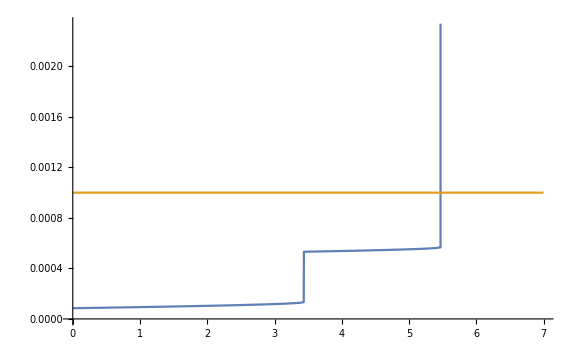

```mathematica
Plot[{v[j],0.001},{j,0,20},ImageSize->Large]
```

```mathematica
FindRoot[v[j]==0.001,{j,1.5},MaxIterations->25]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 25 iterations.

{j→1.}

```mathematica
FindRoot[v[j]==0.001,{j,0.}]
```

{j→1.}

```mathematica
GetParameter[v[#]&,1]
```

{0.497805,1.95871}